# On the Secrecy of Ballot Receipts in E2E Elections

This notebook has some visualization to see the privacy leaked in ThreeBallot receipts. The nodes in the graph are a receipt, where a 0 denotes no mark made for a candidate and a 1 denotes a mark made. The order of the marks correspond to the candidates in alphabetical order: {Alex Jones, Bob Smith} for the two candidate example, {Alex Jones, Bob Smith, Carol Wu} for the three candidate graph. Each line from a receipt to a candidate is equally probable, and as is evident, some receipts are overwhelmly likely to map to one candidate as opposed to another. This is non-negligible information.

These results are from the following paper:
http://www.cs.uwaterloo.ca/~j5clark/papers/BallotReceipts.pdf

The highlights are in two blog posts:
http://jeremyclark.wordpress.com/2007/06/12/why-threeballot-receipts-leak-privacy-information/
http://jeremyclark.wordpress.com/2007/06/24/futher-comments-on-threeballot/

## ThreeBallot

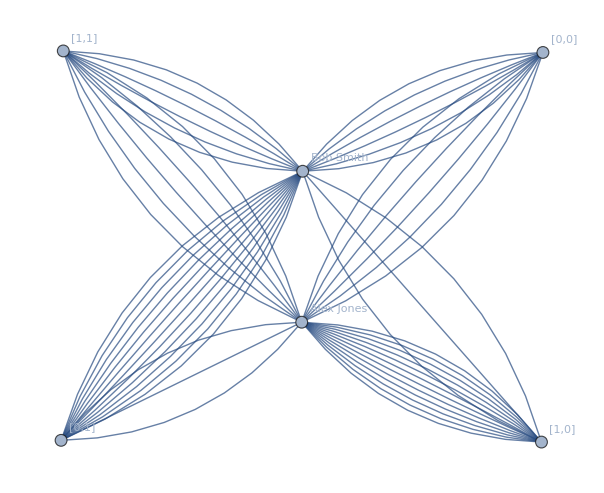

```mathematica
Tuples[{{"[0,0]","[0,1]","[1,0]","[1,1]"},{"Alex Jones","Bob Smith"}}];
paths=(Rule@@#1&)/@%;
probs={6,6,3,12,12,3,6,6};
fullpaths={};
f[i_]:=AppendTo[fullpaths,ConstantArray[paths[[i]],probs[[i]]]];
f/@Range[Length[paths]];
Flatten[fullpaths];

GraphPlot[%,VertexLabeling->True,DirectedEdges->False,MultiedgeStyle->0.2]
Export["a.jpg",%];
```

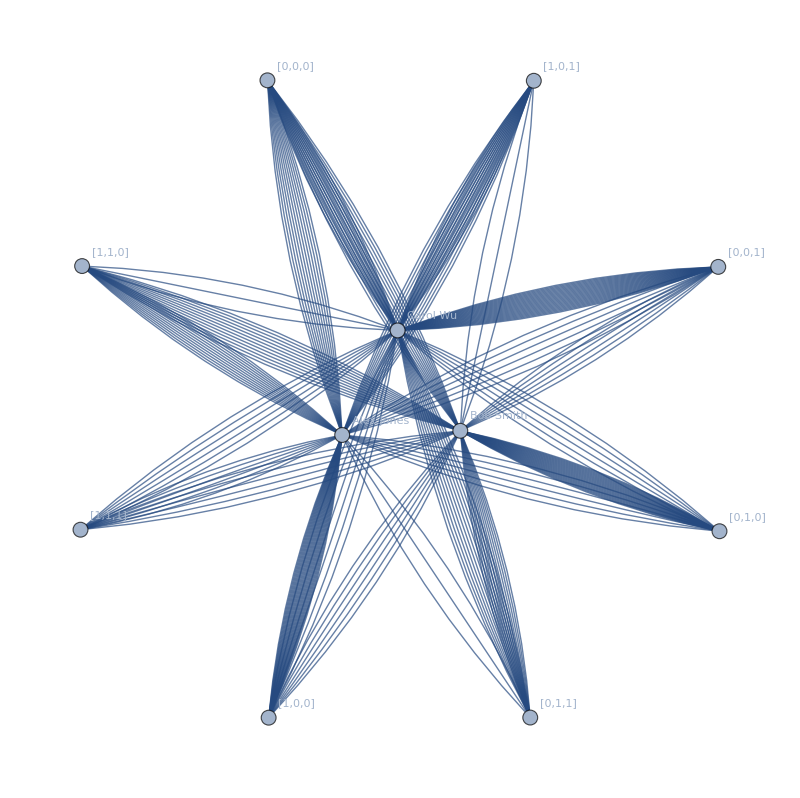

```mathematica
Tuples[{{"[0,0,0]","[0,0,1]","[0,1,0]","[0,1,1]","[1,0,0]","[1,0,1]","[1,1,0]","[1,1,1]"},{"Alex Jones","Bob Smith","Carol Wu"}}];
paths=(Rule@@#1&)/@%;
probs={12,12,12,6,6,24,6,24,6,3,12,12,24,6,6,12,3,12,12,12,3,6,6,6};
fullpaths={};
f[i_]:=AppendTo[fullpaths,ConstantArray[paths[[i]],probs[[i]]]];
f/@Range[Length[paths]];
Flatten[fullpaths];

GraphPlot[%,VertexLabeling->True,DirectedEdges->False,MultiedgeStyle->0.07,ImageSize->800]
Export["b.jpg",%];
```

## Pret a Voter

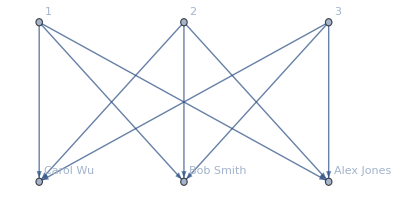

```mathematica
Tuples[{{1,2,3},{"Carol Wu","Bob Smith","Alex Jones"}}];
(Rule@@#1&)/@%;
LayeredGraphPlot[%,VertexLabeling->True,DirectedEdges->True]
```

## Punchscan

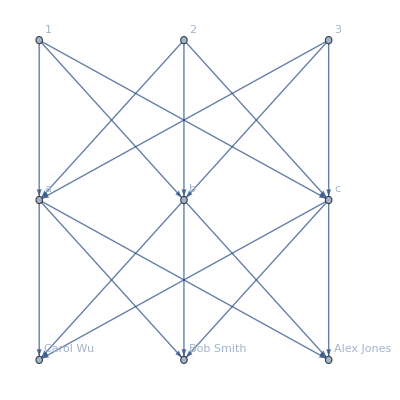

```mathematica
{Tuples[{{1,2,3},{"a","b","c"}}],Tuples[{{"a","b","c"},{"Carol Wu","Bob Smith","Alex Jones"}}]};
Flatten[%,1];

(Rule@@#1&)/@%;
LayeredGraphPlot[%,VertexLabeling->True,DirectedEdges->True]
```